## Partition the alphabet into optimal groups

(I start off every notebook with this command to clear the variables that might be hanging around from a different Notebook)

```mathematica
Clear["Global`*"];
```

Load the data we computed earlier and take a peak

```mathematica
percents = CloudGet["https://www.wolframcloud.com/objects/e338adb3-f090-4867-8456-f3f66c422f38"];
Short[percents, 2]
```

<|A→0.0379425,B→0.0850223,C→0.077475,D→0.0453413,«19»,X→0.000384696,Y→0.00634222,Z→0.00566274|>

Calculate and chart the cumulative percentages

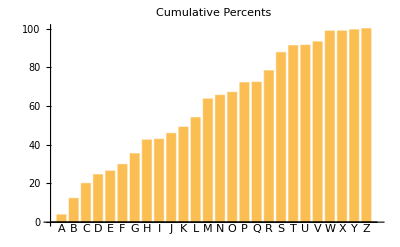

```mathematica
alphabet = Keys@percents;
cumulative = 100. * Rest@FoldList[Plus, 0, Values@percents];
BarChart[cumulative, ChartLabels->alphabet,PlotLabel->"Cumulative Percents"]
```

Now calculate the optimal break points for n_ groups by taking the values above and looks for values closest to 1/n, 2/n ... n/n

```mathematica
n = 4;
breaks = List[];
Do[(
	target = 100. * i / n; (* 0.25, 0.5, 0.75, 1 *)
	adjusted = Abs[cumulative - target]; (* distance from a multiple of 0.25 *)
	closest = Min@adjusted;
	index = First@Flatten@Position[adjusted, _?(Abs[Abs[#] - closest] < 0.0001 &)];
	(* Very small differences in floating points makes looking for very small margins safer *)
	breaks = Append[breaks, index];
), { i, 1, n }];
lengths = breaks - Most[Prepend[breaks, 0]]
```

{4,7,6,9}

Now divide up the values and letters into the groups we just calculated

```mathematica
startIndices = Most@FoldList[Plus, 1, lengths];
endIndices = Rest@FoldList[Plus, 0, lengths];
indexRanges = Transpose[{startIndices, endIndices}];
letterGroups = Take[alphabet, { First@#, Last@# }]& /@ indexRanges;
valueGroups = Take[Values@percents, { First@#, Last@# }]& /@ indexRanges;
rangeLabels = First@# <> "-" <> Last@#& /@ letterGroups
```

{A-D,E-K,L-Q,R-Z}

To map colors to the groups, we need an association that points the values to the colors

```mathematica
colors = Flatten[ConstantArray[First@#, Last@#]& /@ Transpose[{{Darker@Red, Orange, Darker@Yellow, Darker@Green}, lengths}]];
colorLookup = AssociationThread[Values@percents, colors];
```

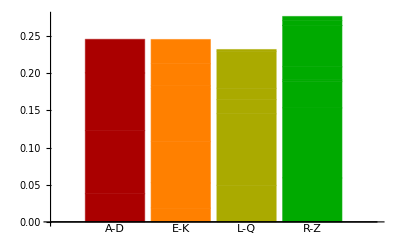

```mathematica
BarChart[valueGroups,
	ChartLayout->"Stacked",
	ColorFunction -> Function[v, colorLookup[v]],
	ColorFunctionScaling->False,
	ChartLabels->{ rangeLabels, None}
]
```